```mathematica
data = Import["/Users/philliphuang/Desktop/d0.xlsx"]
```

{{{128.,0.00018425},{256.,0.000452},{512.,0.0016415},{1024.,0.00416475},{2048.,0.008332},{4096.,0.0259115},{8192.,0.0686638},{16384.,0.16413},{32768.,0.380224},{65536.,0.829719},{131072.,1.81754}}}

```mathematica
nlm=NonlinearModelFit[data[[1]],b*x* Log[x]^a,{a,b,c},x]
```

FittedModel[2.99123×10^-7 x Log[x]^1.55558]

```mathematica
nlm["BestFit"]
```

2.99123×10^-7 x Log[x]^1.55558

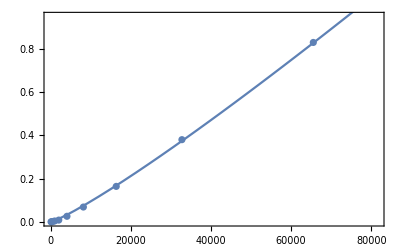

```mathematica
Show[ListPlot[data],Plot[nlm[n],{n,0,150000}],Frame->True]
```

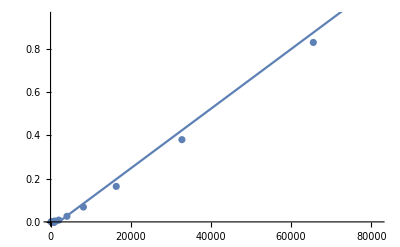

```mathematica
Show[ListPlot[data],Plot[model["BestFit"],{n,0,150000}]]
```

```mathematica
Plot[m["BestFit"],{x,0,150000}]
```

-Graphics-